Original variables

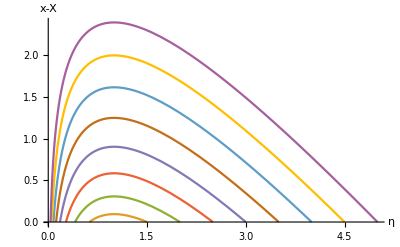

```mathematica
Plot[
Table[-(y-y0)+1Log[y/y0],{y0,1,5,0.5}]//Evaluate,
{y,-1,6},PlotRange->{All,{0,Automatic}},
AxesLabel->{"η","x-X"}]
```

```mathematica
s=Integrate[1/y √(2 y^2-2β y+β^2),y]//Simplify
t[y_]=Log[y];
```

√(25-10 y+2 y^2)+(5 ArcSinh[1-(2 y)/5])/(√2)+5 Log[y]-5 Log[5-y+√(25-10 y+2 y^2)]

```mathematica
yf[y0_,β_]:=Threshold[{Re[y/.FindRoot[y-y0==β Log[y/y0],{y,0.1}]]}]
```

```mathematica
Manipulate[
Plot[{yf[y0,ββ]},
{y0,ββ,20ββ},PlotRange->{{0,20ββ},{0,ββ}}],
{ββ,1,100}]
```

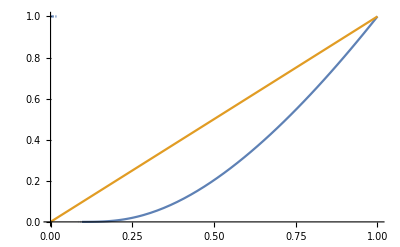

-√(2-2 a+a^2)+√(a^2-2 a zf+2 zf^2)+a Log[-1+a+√(2-2 a+a^2)]+(a Log[2-a+√2 √(2-2 a+a^2)])/(√2)+a Log[zf]-a Log[a-zf+√(a^2-2 a zf+2 zf^2)]-(a Log[-a+2 zf+√2 √(a^2-2 a zf+2 zf^2)])/(√2)

```mathematica
Plot[{x/.FindRoot[α Log[x]==x-1,{x,0.5*α}],α},
{α,0,1}]
```

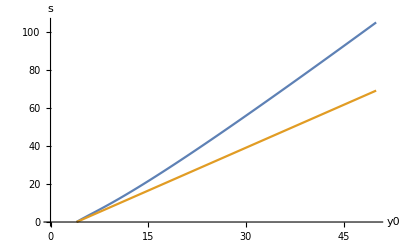

```mathematica
β=4;
Plot[{(s/.y->y0)-(s/.y->yf[y0,β]),1.5{y0-β}},
{y0,β,50},
PlotRange->{{0,Automatic},All},
AxesLabel->{"y0","s"}]
```

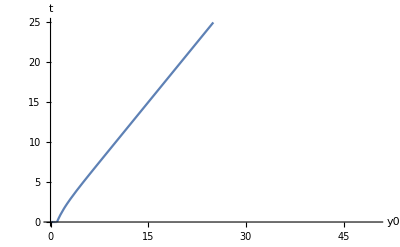

```mathematica
β=1;
Plot[t[y0]-t[yf[y0,β]],
{y0,0,50},
PlotRange->{{0,50},{0,25}},
AxesLabel->{"y0","t"}]
```

```mathematica
Plot3D[√(a^2-2a z+2 z^2)/√(a^2-2a+2),{a,0,1},{z,0,a}]
```

-Graphics3D-

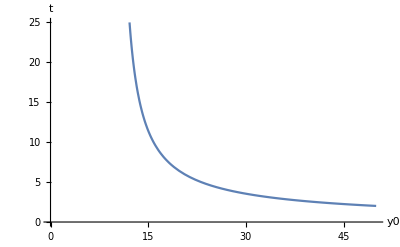

```mathematica
β=10;
Plot[β/(t[y0]-t[yf[y0,β]]),
{y0,β,50},
PlotRange->{{0,50},{0,25}},
AxesLabel->{"y0","t"}]
```

(un)Natural variables

```mathematica
Δζ[ξ_,α_]:=α Log[ξ]-ξ+1
```

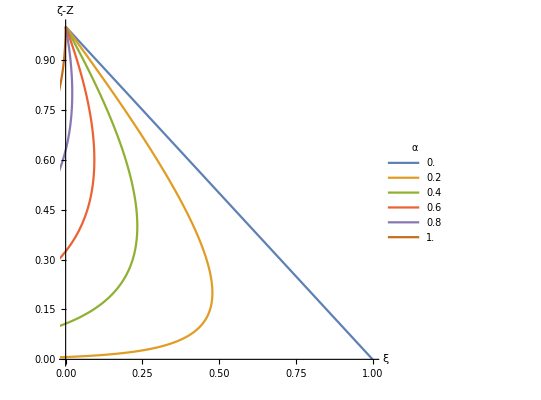

```mathematica
ParametricPlot[
Table[{Δζ[ξ,α],ξ},{α,0,1,0.2}]//Evaluate,
{ξ,0,1},PlotRange->{{0,1},{0,1}},
AxesLabel->{"ξ","ζ-Ζ"},
PlotLegends->LineLegend[Table[α,{α,0,1,0.2}],LegendLabel->"α"]]
```

```mathematica
ξf[α_]:=Threshold[{Re[
ξ/.FindRoot[Δζ[ξ,α]==0,{ξ,α/100}]
]}]
```

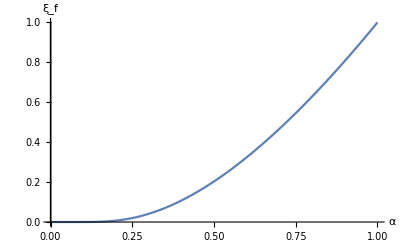

```mathematica
Plot[ξf[α],{α,0,1},
AxesLabel->{"α","ξ_f"}]
```

```mathematica
σ[α_,ξ_]:=Assuming[1≥α≥0&&1>ξ>0,
-Integrate[√((α/ξ-1)^2+1),{ξ,1,ξ}]]//Evaluate//Simplify
σ[α,ξ]
```

√(2-2 α+α^2)-√(α^2-2 α ξ+2 ξ^2)-α Log[-1+α+√(2-2 α+α^2)]-(α Log[2-α+√2 √(2-2 α+α^2)])/(√2)-α Log[ξ]+α Log[α-ξ+√(α^2-2 α ξ+2 ξ^2)]+(α Log[-α+2 ξ+√2 √(α^2-2 α ξ+2 ξ^2)])/(√2)

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Infinity::indet: Indeterminate expression 0.\ (-∞) encountered.

{Indeterminate,Indeterminate,Indeterminate,2.02124,1.92924,1.84572,1.76892,1.69768,1.63118,1.56878,1.51,1.45443,1.40173,1.3516,1.3038,1.25808,1.21423,1.17207,1.13142,1.09212,1.05401,1.01694,0.980795,0.945435,0.910743,0.876606,0.842919,0.809584,0.776507,0.743602,0.710791,0.678001,0.645165,0.612223,0.57912,0.545806,0.512238,0.478376,0.444186,0.409637,0.3747,0.339353,0.303573,0.267344,0.230647,0.19347,0.155801,0.117627,0.0789411,0.0397343,1.96978×10^-8}

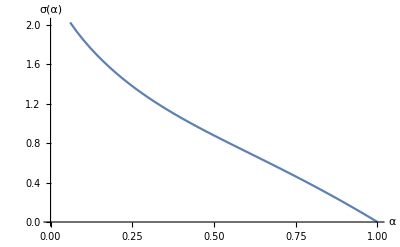

```mathematica
αlist=Table[α,{α,0,1,0.02}];
flist=ξf/@αlist//Flatten;
flist[[1]]=0;
σlist=σ[α,ξf]/.{α->αlist,ξf->flist}
ListLinePlot[Transpose[{αlist,σlist}],
AxesLabel->{"α","σ(α)"}]
```

```mathematica
τ[ξ_]:=Log[1/ξ]
```

```mathematica
pltτ=ListLinePlot[Transpose[{αlist,τ/@flist}],
AxesLabel->{"α","τ"}]//Quiet;
pltlnτ=ListLogPlot[Transpose[{αlist,τ/@flist}],
Joined->True,
AxesLabel->{"α","τ"}]//Quiet;
```

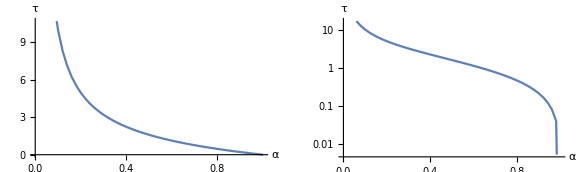

```mathematica
GraphicsRow[{pltτ,pltlnτ},ImageSize->Large]
```